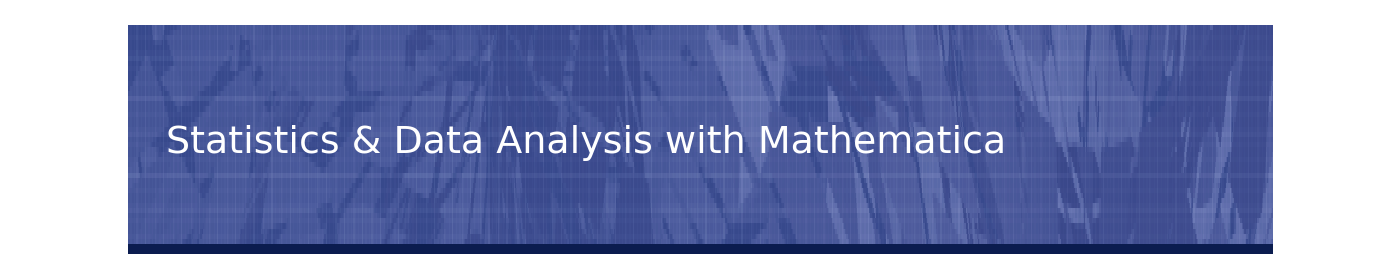
# 

## Presenter

Harry Calkins
seminars@wolfram.com

## Online

DayName, Day MonthName Year

## Overview

The following areas will be discussed:

Descriptive and exploratory statistics: descriptive measures, counting, charts, smoothing, transformations, clustering

Symbolic distributions: properties of distributions, random number generation, visualization

Model fitting and analysis: linear regression, nonlinear regression, generalized linear models including logit and probit, ANOVA, local and global optimization

Related graphics, data import, data operations and general symbolic and numeric computation will be seen in the context of examples.

### Overview Data accessibility

Data that is to be analyzed often needs to be obtained from some external source.

File import/export

The Import and Export functions can import or export dozens of different file formats including numeric and tabular formats, plain or formatted text, and graphics formats.

A few formats of particular note for numeric data analysis include XLS, CSV, TSV, DBF, and MDB, but there are many others as well.

Available formats can be displayed by evaluating $ImportFormats and $ExportFormats.

```mathematica
{$ImportFormats//Length,$ExportFormats//Length}
```

Databases

DatabaseLink, included in Mathematica, allows users to integrate Mathematica with database management systems.  DatabaseLink is JDBC-compliant and works with all known databases.  It contains both a SQL and a Mathematica interface.

## Descriptive Statistics

Many descriptive statistics are included in Mathematica 7.

Here are 20 uniformly distributed random numbers between 0 and 10.

```mathematica
data=RandomReal[10,20]
```

This gives descriptive measures of data based on the first 4 moments.

```mathematica
{Mean[data],Variance[data],Skewness[data],Kurtosis[data]}
```

The data can be visualized as a sequence using ListPlot.

```mathematica
ListPlot[data]
```

### Descriptive Statistics Descriptive charts

Graphics are extremely useful for understanding characteristics of data. Histograms, bar charts, pie charts, and more generalized sector and rectangle charts are newly added Mathematica 7.

This gives default bar and pie charts for some frequency data.

```mathematica
GraphicsRow[{BarChart[{5,2,10,4,6}],PieChart[{5,2,10,4,6}]},ImageSize-> Large]
```

Numerous options are available for modifying the styles and appearance of these charts.

```mathematica
BarChart[{5,2,10,4,6},BarOrigin->Left,ChartStyle->"DarkRainbow",ChartLabels->{"John","Mary","Bob","Sally","Lucy"}]
```

### Descriptive Statistics Descriptive charts

Returning to the random numbers previously generated, histograms and stem and leaf plots might be used to see the general distribution of values.

This gives a histogram of the data.

```mathematica
Histogram[data,5]
```

StemLeafPlot is defined in the Statistical Plots package included with Mathematica.

```mathematica
Needs["StatisticalPlots`"]
```

```mathematica
StemLeafPlot[data]
```

### Descriptive Statistics Additional measures

Additional measures of location and dispersion, quantile-based measures, and more general measures such as CentralMoment are included.

```mathematica
tooltipped[color_,fun_]:=With[{val=fun[data]},{color,Tooltip[Line[{{0,val},{20,val}}],fun]}]
```

```mathematica
ListPlot[data,Epilog->MapThread[tooltipped,{{Red,Green,Blue},{Median,RootMeanSquare,GeometricMean}}]]
```

```mathematica
{StandardDeviation[data],MeanDeviation[data],MedianDeviation[data]}
```

```mathematica
Quantile[data,.6]
```

```mathematica
InterquartileRange[data]
```

A box-and-whisker plot can be used to visualize the spread of the data.

```mathematica
Needs["StatisticalPlots`"]
```

```mathematica
BoxWhiskerPlot[data]
```

### Descriptive Statistics Descriptive measures with matrices

Descriptive functions also work on matrix data, returning the descriptive measures for columns.

```mathematica
multidata=RandomReal[10,{125,3}];
```

```mathematica
Show[{ListPointPlot3D[multidata],Graphics3D[{PointSize[Large],Red,Point[Mean[multidata]],Green,Point[Median[multidata]],Orange,Point[SpatialMedian[multidata]]}]}]
```

```mathematica
MedianDeviation[multidata]
```

```mathematica
Quantile[multidata,.6]
```

### Descriptive Statistics Covariance and correlation

The covariance and correlation between two lists of numbers can be computed.

```mathematica
data2=RandomReal[10,20]
```

```mathematica
Covariance[data,data2]
```

```mathematica
Correlation[data,data2]
```

A side-by-side stem-and-leaf plot can be used to compare two univariate data sets.

```mathematica
StemLeafPlot[data,data2]
```

Covariance and correlation matrices can also be computed for matrices.

```mathematica
Covariance[multidata]//MatrixForm
```

```mathematica
Correlation[multidata]//MatrixForm
```

Some additional multivariate measures are included in the Multivariate Statistics package.

### Descriptive Statistics Multivariate visualization

Numerous visualization functions are included for visualizing multivariate data including histograms, point and bubble plots.

This gives a histogram for the first two dimensions of the multivariate data, and a histogram for 10000 bivariate normal points.

```mathematica
GraphicsRow[{Histogram3D[multidata[[All,1;;2]],5],Histogram3D[RandomReal[NormalDistribution[],{5000,2}]]},ImageSize-> Large]
```

Here the trivariate data are visualized as points and as bubbles with size based on the z-coordinate.

```mathematica
GraphicsRow[{ListPointPlot3D[multidata,PlotStyle->PointSize[.025]],BubbleChart[multidata,BubbleScale-> "Diameter",BubbleSizes-> {.025,.075}]},ImageSize-> Large]
```

Four-dimensional data can be visualized as a three-dimensional bubble chart.

```mathematica
BubbleChart3D[RandomReal[10,{25,4}],ColorFunction-> "AvocadoColors"]
```

### Descriptive Statistics Counting functions

Counting based on some categorization often provides a useful description of data.

This counts continuous data in bins of width 2 from 0 to 10.

```mathematica
BinCounts[data,{0,10,2}]
```

Here explicit cutoffs of 0, 4, 5, 9, and 10 are used.

```mathematica
BinCounts[data,{{0,4,5,9,10}}]
```

Multidimensional data can be counted in bins of appropriate dimension.

```mathematica
BinCounts[multidata,{0,10,5},{0,10,5},{0,10,5}]
```

### Descriptive Statistics Counting functions

For discrete or nominal data, it is often useful to compute counts for the distinct values.

Tally counts the frequencies of distinct elements

```mathematica
tallies=Tally[RandomChoice[{a,b,c,d},24]]
```

```mathematica
BarChart3D[tallies[[All,2]],ChartLabels->(Style[#,24]&/@tallies[[All,1]])]
```

Commonest gives a list of the most frequently occurring elements.

```mathematica
Commonest[{c,a,b,a,d,c,c,b,a}]
```

The Count function can be used to obtain more general counts based on a pattern.

For instance, the number of occurrences of a particular element in a list or the number of even numbers in a list of integers might be counted.

```mathematica
Count[{c,a,b,a,d,c,c,b,a},b]
```

```mathematica
Count[{3,2,1,4,1,5,3,3,4,3},_?EvenQ]
```

### Descriptive Statistics Data transformation

Built-in smoothers include MovingAverage, MovingMedian, and ExponentialMovingAverage. Data can be shifted and scaled using Standardize, and a new set of filters of particular interest for image analysis has been added in Mathematica 7.

This gives a two-term moving median.

```mathematica
MovingMedian[data,3]
```

```mathematica
ListPlot[{data[[2;;-2]],MovingMedian[data,3]},Joined-> {False,True}]
```

Weighted moving averages can be obtained by giving a list of weights.

```mathematica
MovingAverage[data,{1/3,2/3,1/3,1/2}]
```

Standardize shifts by the mean and scales by the standard deviation by default.

```mathematica
Standardize[data]
```

Image-related filters adjust at the ends to maintain the data length or dimensions.

```mathematica
ListPlot[{data,MeanFilter[data,3]},Joined-> {False,True}]
```

Other smoothers and transformations can be constructed using functions such as ListCorrelate and ListConvolve, and arithmetic and linear algebra functions.

### Descriptive Statistics Data transformation via linear algebra

As an example of using linear algebra to perform a transformation, we consider the Mahalanobis transform which transforms multivariate data to uncorrelated data with mean 0 and unit variances.

A Mahalanobis transform of multivariate data can be performed directly with a little linear algebra.

```mathematica
chol=CholeskyDecomposition[Inverse[Covariance[multidata]]]
```

```mathematica
Short[decorrelated=Transpose[Transpose[multidata]-Mean[multidata]].Transpose[chol],6]
```

The transformed data are decorrelated with mean 0 and unit variances up to numerical error.

```mathematica
Mean[decorrelated]
```

```mathematica
Covariance[decorrelated]//MatrixForm
```

### Descriptive Statistics Clustering data

Clustering of data is often used to separate data into groups, or to try to identify subgroups within a data set.

The main clustering function is FindClusters, which can be used on numeric, binary/Boolean, or string data.  A number of distance and dissimilarity functions are also included and can be found here.

This gives the Euclidean, Manhattan and Chessboard distance between two vectors.

```mathematica
Through[{EuclideanDistance,ManhattanDistance,ChessboardDistance}[{1,2,3,4,5},{2.3,7,4.2,1.3,10}]]//Column
```

This gives a Boolean dissimilarity between two binary vectors.

```mathematica
DiceDissimilarity[{1,0,1,0,0,1,0},{0,0,1,1,0,0,0}]
```

This gives the edit distance between two strings.

```mathematica
EditDistance["This is a string.","This string is different."]
```

Used with FindClusters, these define measures for separating data.

### Descriptive Statistics Numeric clustering example

As an example, we will start with 10 clusters that are samples from bivariate normal distributions.

```mathematica
Needs["MultivariateStatistics`"]
```

```mathematica
origclusters=BlockRandom[SeedRandom[123456789];
muvals=RandomReal[{-10,10},{10,2}];
sigmavals=Table[Block[{s1=RandomReal[],s2=RandomReal[],s12},
s12=RandomReal[]*Sqrt[s1*s2];
{{s1,s12},{s12,s2}}],{10}];
Join[MapThread[RandomReal[MultinormalDistribution[#1,#2],RandomInteger[{20,75}]]&,{muvals,sigmavals}]]];
```

Plotting the data shows the original clusters of the data.

```mathematica
ListPlot[origclusters]
```

Next we will mix up the elements of the original data so the data are not already grouped, and use FindClusters to identify clusters in the data.

```mathematica
newclusters=BlockRandom[SeedRandom[1];RandomSample[Flatten[origclusters,1]]];
```

```mathematica
clusters=FindClusters[newclusters];
```

FindClusters identifies 3 distinct clusters, which looks quite reasonable given the scatter of the data.

```mathematica
Length[clusters]
```

### Descriptive Statistics Visualization of clusters

For numeric data in up to three dimensions, the clusters are easy to visualize with list plotting functions.

```mathematica
GraphicsRow[{ListPlot[origclusters],ListPlot[clusters]},Frame-> All,FrameStyle-> Thick]
```

The desired number of clusters can be specified if that number is known.

```mathematica
ListPlot[FindClusters[newclusters,4]]
```

### Descriptive Statistics Cluster hierarchies

A cluster hierarchy can also be visualized using dendrogram plots. The Hierarchical Clustering package is needed for this type of visualization.

```mathematica
Needs["HierarchicalClustering`"]
```

Here is some example text, split into string elements.

```mathematica
textdata=StringSplit["This talk will give a broad overview of statistics in Mathematica. Statistics functions and other technologies, such as import/export capabilities and visualization functions, as they relate to statistical computation will be discussed."];
```

The following generates a dendrogram labeling the leaves with the string elements they represent.

```mathematica
Show[DendrogramPlot[textdata,LeafLabels->(#&),Orientation->Left],ImageSize-> Large]
```

## Symbolic Distributions

A total of 39 univariate continuous and discrete distributions are built into the kernel.  An additional 8 distributions derived from multivariate distributions are included in the Multivariate Statistics package.

Newly added distributions in Mathematica 7 include InverseChiSquareDistribution, InverseGammaDistribution, and LevyDistribution. StudentTDistribution and MultivariateStudentTDistribution have been extended to include location and scale parameters.

### Symbolic Distributions Distribution properties

Many properties of distributions such as PDF, CDF, mean, variance and characteristic function are available.

This gives moment-based measures for a noncentral χ^2 distribution.

```mathematica
{Mean[NoncentralChiSquareDistribution[ν,λ]],Variance[NoncentralChiSquareDistribution[ν,λ]],Skewness[NoncentralChiSquareDistribution[ν,λ]],Kurtosis[NoncentralChiSquareDistribution[ν,λ]]}
```

General expectations can be computed as well.  Here is the n^th raw moment of a Poisson distribution.

```mathematica
ExpectedValue[x^n,PoissonDistribution[μ],x]
```

This is the characteristic function of a Laplace distribution.

```mathematica
CharacteristicFunction[LaplaceDistribution[μ,β],t]
```

### Symbolic Distributions Visualization

Functions for plotting functions can be useful for visualizing symbolic properties of distributions, such as density functions.

This plots the cumulative distribution function for a gamma distribution.

```mathematica
Plot[CDF[GammaDistribution[3,5],x],{x,0,50}]
```

This shows the probability mass function for a binomial distribution.

```mathematica
DiscretePlot[PDF[BinomialDistribution[20,.3],i],{i,0,20}]
```

This plots the density for a bivariate t-distribution.

```mathematica
Needs["MultivariateStatistics`"]
```

```mathematica
Plot3D[PDF[MultivariateTDistribution[{{1,1/2},{1/2,1}},20],{x,y}],{x,-3,3},{y,-3,3}]
```

### Symbolic Distributions Random number generation

Random numbers can be generated from each of the defined distributions. They are obtained using RandomReal for continuous distributions and RandomInteger for discrete distributions.

Random elements can be generated one at a time or in a list or tensor of arbitrary dimension.

```mathematica
RandomInteger[GeometricDistribution[1/3]]
```

```mathematica
Show[{Histogram[RandomInteger[GeometricDistribution[1/3],500],{-1/2,39/2,1},"ProbabilityDensity"],DiscretePlot[PDF[GeometricDistribution[1/3],n],{n,0,20}]},ImageSize-> Large]
```

```mathematica
RandomInteger[GeometricDistribution[1/3],{2,3,3}]
```

Elements from continuous distributions can also be generated in arbitrary precision.

```mathematica
RandomReal[GammaDistribution[1/2,4],WorkingPrecision->20]
```

The same holds for multivariate distributions.

```mathematica
mu={1,2,3,4};
sigma=({{8, 12.5, -6, -1}, {12.5, 27, 0.5, -4}, {-6, 0.5, 25, -3}, {-1, -4, -3, 1.4}});
```

This give a random observation from a four-dimensional normal distribution.

```mathematica
Needs["MultivariateStatistics`"]
```

```mathematica
RandomReal[MultinormalDistribution[mu,sigma]]
```

The correlations between dimensions can be visualized using a pairwise scatter plot.

```mathematica
Needs["StatisticalPlots`"]
```

```mathematica
PairwiseScatterPlot[RandomReal[MultinormalDistribution[mu,sigma],100]]
```

Additional random functions include RandomChoice, RandomSample, RandomComplex, and RandomPrime for sampling with replacement, sampling without replacement, complex numbers, and primes, respectively.

## Model Fitting and Analysis

Mathematica 7 adds a new framework and functionality for linear and nonlinear regression: logit, probit, and generalized linear models. An extensive set of optimization functions, linear algebra functions and a package for analysis of variance (ANOVA) all provide capabilities of interest in model fitting and analysis.

### Model Fitting and Analysis Linear regression

Here we import some data from an Excel spreadsheet.

```mathematica
lineardata=Import[FileNameJoin[{NotebookDirectory[],"linearfitdata.xls"}],{"Sheets",1}]
```

The data can be fitted to a linear model using LinearModelFit.

```mathematica
lm=LinearModelFit[lineardata,{x,y,z},{x,y,z}]
```

```mathematica
Normal[lm]
```

LinearModelFit produces a FittedModel object from which diagnostics and results and be obtained.

A list of available results can be obtained by asking for the "Properties".

```mathematica
lm["Properties"]
```

### Model Fitting and Analysis Linear regression diagnostics

Individual properties or lists of properties can be obtained in the same manner.

Here the standardized residuals and Cook’s distances are extracted.

```mathematica
{stresids,cookd}=lm[{"StandardizedResiduals","CookDistances"}]
```

In a linear regression, we might wish to look at plots of the standardized residuals and Cook’s distances to assess approximate normality of errors and influence of individual points.

```mathematica
GraphicsRow[{ListPlot[stresids],ListPlot[cookd,Filling->Bottom,PlotRange->All]},ImageSize-> Large]
```

Residuals can also be viewed against predictors to check for systematic trends which would violate the model assumptions.

```mathematica
GraphicsRow[With[{resids=lm["FitResiduals"]},
Table[ListPlot[Transpose[{lineardata[[All,i]],resids}],Frame->True,FrameLabel->{{x,y,z}[[i]],"residual"}],{i,3}]],ImageSize-> 12 72]
```

### Model Fitting and Analysis Linear regression function evaluation

FittedModel objects can also be evaluated at a point.

Here the fitted function is evaluated for particular values of x, y, and z.

```mathematica
lm[1.5,3,2]
```

This plots the fitted function when z=1.

```mathematica
Plot3D[lm[x,y,1],{x,0,5},{y,0,5}]
```

### Model Fitting and Analysis Linear regression tables

Common tabular results can be obtained.

Here are analysis of variance and parameter tables for the fitted model.

```mathematica
Column[StyleTable[#,{FontSize->18}]&/@lm[{"ANOVATable","ParameterTable"}],Frame-> All]
```

Unformatted tabular results are also available.

These are the entries from the ANOVA table and the parameter table.

```mathematica
lm["ANOVATableEntries"]
```

```mathematica
lm["ParameterTableEntries"]
```

Quantities from the tables, such as mean squares and t-statistics, can also be extracted for use in further computations.

```mathematica
lm[{"ANOVATableMeanSquares","ParameterTStatistics"}]
```

### Model Fitting and Analysis Generalized linear models (GLM)

For linear regression, the model is of the form

ŷ=β_0+β_1 f_1+β_2 f_2+…

for basis functions f_1, f_2, …. Each observed y_i is assumed to be from a normal distribution with mean OverHat[y_i].

For generalized linear models, the model is of the form

ŷ=g^-1(β_0+β_1 f_1+β_2 f_2+…)

where g is an invertible function called the link function, and each observed y_i is assumed to be from an exponential family distribution with mean OverHat[y_i]. Special cases include linear, logistic and probit regression, log-linear models for count data, and gamma and inverse Gaussian models. Note that the errors are not independent of the y values.

Built- functions for generalized linear model include:

LinearModelFit: linear regression

LogitModelFit: logistic regression

ProbitModelFit: probit regression

GeneralizedLinearModelFit: generalized linear models with specified distributional structures and links

Each of these functions supports continuous and nominal predictor variables.

### Model Fitting and Analysis GLM: logit and probit models

Logit and probit models are commonly used to model probabilities. The observed probabilities are assumed to be success probabilities realized from binomial distributions. Logit and probit models can be fitted via the LogitModelFit and ProbitModelFit functions.

Here is some data with responses written as number of successes over number of trials.

```mathematica
binomdata={{1,3/8},{1.5,2/10},{2.1,4/6},{2.5,3/7},{3.4,8/11},{4,12/14}}
```

The fractions are treated as probabilities.

```mathematica
logit1=LogitModelFit[binomdata,x,x]
```

Weights can be used to incorporate the number of trials, in this case the denominators of the probabilities.

```mathematica
logit2=LogitModelFit[binomdata,x,x,Weights->{8,10,6,7,11,14}]
```

### Model Fitting and Analysis GLM: logit and probit models

The functional form as well as numerous results for a fitted function can be obtained from the FittedModel as was the case for linear models.

The fitted models with and without weights differ somewhat.

```mathematica
Row[{Normal[logit1],"   ",Normal[logit2]}]
```

The available properties differ somewhat from those for linear models.

```mathematica
logit1["Properties"]
```

Here are the parameter tables for the two logit models.

```mathematica
{logit1["ParameterTable"],logit2["ParameterTable"]}
```

### Model Fitting and Analysis GLM: logit and probit models

ProbitModelFit is the analogous function for probit models. The general features and available results are the same as for LogitModelFit.

This is a probit model for the same data.

```mathematica
probit=ProbitModelFit[binomdata,x,x]
```

The difference of the two functions can be plotted to see there is only a small difference between the logit1 and probit fitted functions.

```mathematica
Plot[logit1[x]-probit[x],{x,1,4}]
```

### Model Fitting and Analysis GLM: Poisson count models

Logit and probit models are generalized linear models for probability responses. These models could equivalently be fit via GeneralizedLinearModelFit with "Binomial" ExponentialFamily option and an appropriate choice of LinkFunction.

Models of count data commonly assume Poisson distributed responses. Predictor variables can be continuous (real-valued) or nominal (taking on one of a finite number of distinct names or categories).

Here is some count data for two categorical variables.

```mathematica
countdata={{a,agree,53},{a,disagree,24},{a,undecided,13},{b,agree,78},{b,disagree,48},{b,undecided,110},{c,agree,20},{c,disagree,58},{c,undecided,10},{d,agree,42},{d,disagree,38},{d,undecided,4}};
```

The NominalVariables option can be used to specify which variables are to be treated as nominal.

The default Poisson model is a log-linear model.

```mathematica
loglinmodel=GeneralizedLinearModelFit[countdata,{group,opinion},{group,opinion},ExponentialFamily->"Poisson",NominalVariables->All]
```

As with continuous predictors, the FittedModel can be evaluated at a particular point. Terms arising from nominal variables are represented as DiscreteIndicator functions.

These are the predicted count for group a and agree, and the predicted function for group a.

```mathematica
{loglinmodel[a,agree],loglinmodel[a,opinion]}
```

Other forms of Poisson model can be fitted by specifying a different invertible link function.

This gives a linear Poisson count model.

```mathematica
linmodel=GeneralizedLinearModelFit[countdata,{group,opinion},{group,opinion},ExponentialFamily->"Poisson",NominalVariables->All,LinkFunction->"IdentityLink"]
```

This model is easily visualized using the charting functions.

```mathematica
BarChart[{linmodel[a,#],linmodel[b,#],linmodel[c,#]}&/@{agree,disagree,undecided},ChartElementFunction->"GlassRectangle",ChartLabels->{{"agree","disagree","undecided"},{"a","b","c"}}]
```

### Model Fitting and Analysis GLM: models for other distributions

Linear models with normal or Gaussian errors, binomial logistic and probit models, and log-linear models for counts are among the most widely used generalized linear models. Gamma and inverse Gaussian models are commonly used for positive responses which have much greater variability as the predicted value increases.

The following inputs fit gamma and inverse Gaussian models to the data set used in linear regression earlier.

```mathematica
gammafit=GeneralizedLinearModelFit[lineardata,{x,y,z},{x,y,z},ExponentialFamily->"Gamma"]
```

```mathematica
ivfit=GeneralizedLinearModelFit[lineardata,{x,y,z},{x,y,z},ExponentialFamily->"InverseGaussian"]
```

Gamma models assume an error variance that grows as the square of the predicted value, while inverse Gaussian models assume a cubic relationship. The canonical link function is the reciprocal link for a gamma model and the inverse square link for an inverse Gaussian model. The fitted function is the inverse of the link function applied to the linear combination of basis functions.

Here the linear regression, gamma, and inverse Gaussian fitted functions.

```mathematica
Column[{lm[x,y,z],gammafit[x,y,z],ivfit[x,y,z]}]
```

### Model Fitting and Analysis GLM: non-default links and quasi-likelihood

Any function that is invertible for the response domain can be a valid link function. For instance, the identity link which is the canonical link for Gaussian models (linear regression models) could also be used for gamma or inverse Gaussian model

Here we obtain linear gamma and inverse Gaussian fits for the data.

```mathematica
lineargammafit=GeneralizedLinearModelFit[lineardata,{x,y,z},{x,y,z},ExponentialFamily->"Gamma",LinkFunction->"IdentityLink"]
```

```mathematica
linearivfit=GeneralizedLinearModelFit[lineardata,{x,y,z},{x,y,z},ExponentialFamily->"InverseGaussian",LinkFunction->"IdentityLink"]
```

Note that the parameter estimates differ because the error structure is different for the three linear fits.

```mathematica
Column[{lm[x,y,z],lineargammafit[x,y,z],linearivfit[x,y,z]}]
```

Quasi-likelihood structures can also be used to define the error structure via the variance as a function of the mean. For named distributions, there are quasi-likelihood structures which define the likelihood up to a multiplicative constant. For "Gaussian", "Gamma", and "InverseGaussian" models, the variance functions are 1, μ^2, and μ^3.

The quasi-likelihood versions of normal, gamma and inverse Gaussian models differ only in small numeric differences.

```mathematica
Column[Table[GeneralizedLinearModelFit[lineardata,{x,y,z},{x,y,z},ExponentialFamily->{"QuasiLikelihood","VarianceFunction"->(#^k&)},LinkFunction->"IdentityLink"]//Normal,{k,{0,2,3}}]]
```

### Model Fitting and Analysis Nonlinear regression

The NonlinearModelFit function works for nonlinear least squares models in much the same way the other model fit functions we have just seen work with linear and generalized linear models.

This fits the previously used linear data set to a nonlinear model.

```mathematica
nlm=NonlinearModelFit[lineardata,Sqrt[a*x+b*y*z],{a,b},{x,y,z}]
```

Nonlinear model properties differ somewhat from linear and generalized linear properties.

```mathematica
nlm["Properties"]
```

Here we obtain the functional form of the fitted model.

```mathematica
Normal[nlm]
```

### Model Fitting and Analysis Nonlinear regression: starting values

Fitting nonlinear models requires an iterative process. Choosing good starting values for parameters can be important to get good results. By default all parameters have starting value 1.

Here the model is changed to have a negative sign in front of the coefficient a.

```mathematica
NonlinearModelFit[lineardata,Sqrt[-a*x+b*y*z],{a,b},{x,y,z}]
```

This is really the same model as before except that the sign for the a coefficient is different. In this case the fitting fails because the starting values result in complex numbers. The iterative method would need to pass from positive values of a to negative values with this starting value.

Giving a negative starting value for a gets a good result in this case.

```mathematica
nlm2=NonlinearModelFit[lineardata,Sqrt[-a*x+b*y*z],{{a,-1},{b,5}},{x,y,z}]
```

The estimates are equivalent up to a sign change.

```mathematica
StyleTable[#,{FontSize-> 14}]&/@{nlm["ParameterTable"],nlm2["ParameterTable"]}
```

### Model Fitting and Analysis Nonlinear regression: parameter constraints

Constraints can also be included. Some properties derived from unconstrained distributional assumptions, however, may not be valid.

Here b is constrained to be greater than 15.

```mathematica
nlmc=NonlinearModelFit[lineardata,{Sqrt[a*x+b*y*z],b>15},{a,b},{x,y,z}];
Normal[nlmc]
```

A warning is generated if affected properties are requested. If the estimates are far from the constraint boundaries so that the constraint region covers nearly all of the probability for the parameter vector, results from the unconstrained distributional assumptions are likely fine.

In this case the confidence intervals contain points outside the constraint region.

```mathematica
nlmc["ParameterConfidenceIntervals"]
```

### Model Fitting and Analysis ANOVA

The analysis of variance (ANOVA) model is a categorical linear regression model. While such models can be fit and analyzed using LinearModelFit with NominalVariables, ANOVA provides direct computation of cell means and tests of categorical differences.

Here we import some data from a text file.

```mathematica
anovadata=Import[ToFileName[NotebookDirectory[],"anovadata.txt"],"Table"]
```

The ANOVA function is defined in the ANOVA` package.

```mathematica
Needs["ANOVA`"]
```

By default an ANOVA table and table of cell means are returned.

```mathematica
ANOVA[anovadata,{x,y},{x,y}]
```

The cell means can be omitted and significance tests performed if desired.

This gives an analysis of variance performing Bonferroni and Tukey tests for significant differences between levels of categorical variables.

```mathematica
ANOVA[anovadata,{x,y},{x,y},CellMeans->False,PostTests->{Bonferroni,Tukey}]
```

The same model could be fit using LinearModelFit as follows.

```mathematica
anovalm=LinearModelFit[anovadata,{x,y},{x,y},NominalVariables->All]
```

```mathematica
StyleTable[anovalm["ANOVATable"],{FontSize-> 18}]
```

### Model Fitting and Analysis Optimization functions

Built-in optimization and linear algebra functions are important in their own right, and are heavily used in statistical fitting functions.  These functions can also be used to obtain statistical results that may not be directly built-in.

FindFit finds parameter estimates for a best fit of a model to data, by default using a least squares fit.

```mathematica
FindFit[lineardata,√(a x+b y z),{a,b},{x,y,z}]
```

```mathematica
FindFit[lineardata,{√(a x+b y z),b>15},{a,b},{x,y,z}]
```

NonlinearModelFit gets its parameter estimates from the same internal code as FindFit.

```mathematica
NonlinearModelFit[lineardata,{√(a x+b y z),b>15},{a,b},{x,y,z}]["BestFitParameters"]
```

FindFit also provides for fitting based on other functions of the residual errors, such as total absolute errors.

```mathematica
FindFit[lineardata,√(a x+b y z),{a,b},{x,y,z},NormFunction->(Total[Abs[#1]]&)]
```

### Model Fitting and Analysis Optimization functions

FindMinimum and FindMaximum perform local optimization of an objective function.  NMinimize and NMaximize perform global optimization of an objective function. These functions are particularly useful in statistics when the optimization problem is not easy to define in terms of a model function and a function of residual errors.

For instance, a NormFunction for a maximum likelihood estimate will be quite messy for most distributions.

Here are some data assumed to follow a Weibull distribution.

```mathematica
weibulldata=Import[FileNameJoin[{NotebookDirectory[],"WeibullData.txt"}],"List"]
```

Maximum likelihood estimates of the Weibull parameters can be obtained by maximizing the following log-likelihood function.

```mathematica
wfun[x_,α_,β_] = PDF[WeibullDistribution[α,β],x]
```

```mathematica
loglike[α_?NumericQ,β_?NumericQ]=Total[Map[Log[wfun[#,α,β]]&,weibulldata]];
```

Initial parameter estimates for the optimization can be obtained from a contour plot of the log likelihood function.

```mathematica
ContourPlot[loglike[α,β],{α,1,3},{β,6,9}]
```

Local optimization will suffice in this case and maximum likelihood estimates can then be obtained with reasonable starting values.

```mathematica
FindMaximum[loglike[α,β],{α,2,1,3},{β,8,6,9}]
```

### Model Fitting and Analysis Linear algebra functions

Numerous linear algebra functions such as SingularValueDecomposition and Eigenvalues are important in statistics and in particular in model fitting. A common linear algebra operation is least squares optimization.

Parameter estimates for a least squares fit of a linear model defined by a design matrix and response vector can be obtained directly from the LeastSquares function.

```mathematica
desmat=Transpose[Join[{Table[1,{Length[lineardata]}]},Transpose[lineardata[[All,1;;3]]]]]
```

```mathematica
LeastSquares[desmat,lineardata[[All,-1]]]
```

LinearModelFit gives the same estimate while allowing for additional diagnostics and results.

```mathematica
LinearModelFit[{desmat,lineardata[[All,-1]]}]["BestFitParameters"]
```

There are numerous other applications of linear algebra in model fitting as well.

## Further Resources

Tutorials

Basic Statistics

Continuous Distributions

Discrete Distributions

Descriptive Statistics

Convolutions and Correlations

Curve Fitting

Importing and Exporting Data

Pseudorandom Numbers

Random Number Generation

Numerical Operations on Data

Wolfram Education Group Courses

M215: Applied Statistical Analysis with Mathematica

M221: Introduction to Programming in Mathematica

## Initialization

```mathematica
StyleTable[tbl_Style,rools_List?OptionQ]:=tbl/.Style[x_,"DialogStyle"]:>Style[x,"DialogStyle",Sequence@@rools]
```

```mathematica
SetOptions[ListPlot,{PlotStyle-> PointSize[Medium],ImageSize-> Large}];
```

```mathematica
SetOptions[ListPointPlot3D,PlotStyle-> PointSize[Medium]];
```

```mathematica
SetOptions[DiscretePlot,PlotStyle-> PointSize[Medium]];
```

```mathematica
Needs["StatisticalPlots`"]
```

```mathematica
Needs["MultivariateStatistics`"]
```

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
Needs["ANOVA`"]
```